# Transition from log to power law in the DOS for the M point singularities in the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
17 June 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];

Hamltn1[k1_,k2_,θ_]=W90Data[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

We examine the series expansion at the M point for a particular angle, say 9°

```mathematica
HamTempy[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],9]
```

To find the correct band to series expand, we first compute the eigenvalues at the M point

```mathematica
Sort[Eigenvalues[HamTempy[{0,π//N}]]]
```

{-0.535252,-0.535252,-0.090436,-0.090436,0.289416,0.289416}

Therefore the bands of interest just below the Fermi level are 3 and 4

```mathematica
TaylorExpandBand[HamTempy,{0,π//N},4,4,"Messages"->False]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

{{-0.090436,0,0.0629297 k_x^2-0.0291037 k_y^2,0,-0.040243 k_x^4+0.0265665 k_x^2 k_y^2-0.401383 k_y^4},{-0.090436,0,-0.0291037 k_x^2+0.0629297 k_y^2,0,-0.401383 k_x^4+0.0265665 k_x^2 k_y^2-0.040243 k_y^4}}

## Strategy

As we tune θ, we will find that the series expansion at the M point takes the form α k_x^2+β k_y^2+γ k_x^4+μ k_x^2 k_y^2+ν k_y^4 along with a 90° rotated copy obtained by applying (k_x,k_y)->(-k_y,k_x). 

Since the routine will output the series expansion of the pair of rotated bands together, we need a strategy to isolate a particular band of interest out of the two. Now the series expansion across the range [7°,12°] indicates that ν<<γ for one band and ν>>γ for the other one. Therefore, to be consistent, let us choose the band with ν<γ. The DOS integral is given by

g(ϵ)=∫_BZ d^2 k δ(α k_x^2+β k_y^2+γ k_x^4+μ k_x^2 k_y^2+ν k_y^4-ϵ)

To infer the approximate low energy scaling behaviour of the DOS (particularly for a HOVHS), one normally rescales the k_x and k_y in an appropriate fashion. When α is “small” (to be qualified below) we will rescale (k_x,k_y)->(|ϵ|^(1/4)k_x,|ϵ|^(1/2)k_y) to obtain

g(ϵ)~∫_BZ d^2 k  (|ϵ|)^(1/4+1/2) δ(α|ϵ|^(1/2) k_x^2+β|ϵ| k_y^2+γ|ϵ| k_x^4+μ|ϵ|^(3/2) k_x^2 k_y^2+ν|ϵ|^2 k_y^4-ϵ)

Assume that ϵ>0 (the arguments can be applied with a slight modification for ϵ<0). Then, using the scaling property of the delta function we obtain

g(ϵ)~∫d^2 k ϵ^(1/4+1/2-1) δ(α ϵ^(-1/2) k_x^2+β k_y^2+γ k_x^4+μ ϵ^(1/2) k_x^2 k_y^2+ν ϵ k_y^4-1)

Since [α]=E.l^2 and [γ]=E.l^4, we have [α^2 ϵ^-1]=E.l^4=[γ]. Thus, α^2 ϵ^-1 and γ are comparable since they have the same dimension. In fact, for α^2 ϵ^-1<<γ, we can ignore the k_x^2 term in comparison to the k_x^4 in the DOS integral by further rescaling k_x->k_x/γ^(1/4). (This is what we meant by α being small earlier). For small energies, the terms containing ϵ^(1/2) and ϵ can also be ignored so that the final DOS integral scales approximately as

g(ϵ)∼ϵ^(-1/4) ∫d^2 k δ(β k_y^2+γ k_x^4+ν k_y^4-1),

where the integral is approximately ϵ independent. Thus the crossover from log to power law is controlled by
|ϵ| >>α^2/γ .
That is, for energies above this scale, the quartic term dominates over the quadratic term in the DOS integral giving an approximate power law behaviour.

```mathematica
LogPowerTrans={};
SetSharedVariable[LogPowerTrans];

Do[
HamCurr[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcurr];

Tayl=TaylorExpandBand[HamCurr,{0,π//N},4,4,"Messages"->False];

If[Abs[D[Tayl[[1,5]],{p1,4}]]>Abs[D[Tayl[[1,5]],{p2,4}]],
TaylTrans=Tayl[[1]];
,
TaylTrans=Tayl[[2]];
];

Etrans=1000(Abs[D[TaylTrans[[3]],{p1,2}]^2/D[TaylTrans[[5]],{p1,4}]Factorial[4]/4]);

Print["θ = ",θcurr,"°, Tayl = ",Chop[Total[TaylTrans/.{p1->Subscript[k, x],p2->Subscript[k, y]}],10^-6],"\n\t |ϵ_trans - ϵ_VHS| = ",Etrans," meV."];

AppendTo[LogPowerTrans,{θcurr,Etrans}];

,{θcurr,7,12,0.5}]
```

θ = 7.°, Tayl = -0.050578-0.164322 k_x^2-0.334638 k_x^4+0.0692142 k_y^2+0.033598 k_x^2 k_y^2-0.0594893 k_y^4
	 |ϵ_trans - ϵ_VHS| = 80.6895 meV.

θ = 7.5°, Tayl = -0.0608415-0.130115 k_x^2-0.352663 k_x^4+0.0678727 k_y^2+0.0318845 k_x^2 k_y^2-0.0552582 k_y^4
	 |ϵ_trans - ϵ_VHS| = 48.0057 meV.

θ = 8.°, Tayl = -0.071319-0.0961189 k_x^2-0.369336 k_x^4+0.0661489 k_y^2+0.0298785 k_x^2 k_y^2-0.0499925 k_y^4
	 |ϵ_trans - ϵ_VHS| = 25.0147 meV.

θ = 8.5°, Tayl = -0.0812527-0.0623716 k_x^2-0.385557 k_x^4+0.0644056 k_y^2+0.0280297 k_x^2 k_y^2-0.0447515 k_y^4
	 |ϵ_trans - ϵ_VHS| = 10.0899 meV.

θ = 9.°, Tayl = -0.090436-0.0291037 k_x^2-0.401383 k_x^4+0.0629297 k_y^2+0.0265665 k_x^2 k_y^2-0.040243 k_y^4
	 |ϵ_trans - ϵ_VHS| = 2.11027 meV.

θ = 9.5°, Tayl = -0.0992299+0.00332392 k_x^2-0.415763 k_x^4+0.0615053 k_y^2+0.0251037 k_x^2 k_y^2-0.0358871 k_y^4
	 |ϵ_trans - ϵ_VHS| = 0.0265738 meV.

θ = 10.°, Tayl = -0.108337+0.034718 k_x^2-0.427633 k_x^4+0.059491 k_y^2+0.0228877 k_x^2 k_y^2-0.0302461 k_y^4
	 |ϵ_trans - ϵ_VHS| = 2.81863 meV.

θ = 10.5°, Tayl = -0.11935+0.0651835 k_x^2-0.437599 k_x^4+0.0569053 k_y^2+0.0200521 k_x^2 k_y^2-0.0235761 k_y^4
	 |ϵ_trans - ϵ_VHS| = 9.70955 meV.

θ = 11.°, Tayl = -0.135742+0.094643 k_x^2-0.447995 k_x^4+0.055751 k_y^2+0.0189935 k_x^2 k_y^2-0.0201774 k_y^4
	 |ϵ_trans - ϵ_VHS| = 19.9942 meV.

θ = 11.5°, Tayl = -0.157609+0.122301 k_x^2-0.45859 k_x^4+0.0572222 k_y^2+0.0218601 k_x^2 k_y^2-0.0207123 k_y^4
	 |ϵ_trans - ϵ_VHS| = 32.6163 meV.

θ = 12.°, Tayl = -0.147707+0.149787 k_x^2-0.457987 k_x^4+0.042991 k_y^2+0.0140915 k_x^2 k_y^2+0.0198599 k_y^4
	 |ϵ_trans - ϵ_VHS| = 48.9886 meV.

```mathematica
TransFunc=Interpolation[LogPowerTrans];
```

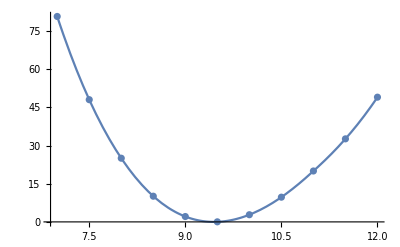

```mathematica
Show[ListPlot[LogPowerTrans],Plot[TransFunc[x],{x,7,12}]]
```

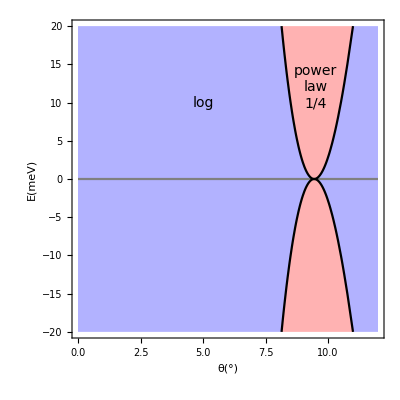

```mathematica
PhasePlt=Plot[{0,Quiet[TransFunc[x]],-Quiet[TransFunc[x]]},{x,0,12},PlotRange->{{0,12},{-20,20}},Axes->False,Frame->True,Filling->{2->{{3},Opacity[0.3,Blue]},2->{Top,Opacity[0.3,Red]},3->{Bottom,Opacity[0.3,Red]}},PlotStyle->{Gray,Black,Black},AspectRatio->1,FrameLabel->{Style["θ(°)",FontSize->14],Style["E(meV)",FontSize->14]}];

Show[PhasePlt(*,Plt1d,Plt1c,Plt1a*),Graphics[Text[Style["log",FontFamily->"Times",FontSize->14],{5,10}]],Graphics[Text[Style["power\nlaw\n1/4",FontFamily->"Times",FontSize->14],{9.5,12}]]]
```